```mathematica
z = PauliMatrix[3];
x = PauliMatrix[1];
I1 = IdentityMatrix[2];
I2 = IdentityMatrix[2^2];
I3 = IdentityMatrix[2^3];
```

```mathematica
H3= -2m(KroneckerProduct[z,I1] + KroneckerProduct[I1,z]) -Δ(KroneckerProduct[x,I1]+ KroneckerProduct[I1,x] + τ KroneckerProduct[x,x])//MatrixForm
```

(-4 m | -Δ | -Δ | -Δ τ
-Δ | 0 | -Δ τ | -Δ
-Δ | -Δ τ | 0 | -Δ
-Δ τ | -Δ | -Δ | 4 m)

```mathematica
Ham = H3/. {τ->1}
```

(-4 m | -Δ | -Δ | -Δ
-Δ | 0 | -Δ | -Δ
-Δ | -Δ | 0 | -Δ
-Δ | -Δ | -Δ | 4 m)

```mathematica
δ=Range[0,2,.1];
```

```mathematica
Table[{Eigenvalues[Ham,1]/.{Δ->d2}}+2 m^2,{d2,δ}]
```

{{2 m^2+Eigenvalues[(-4 m | 0. | 0. | 0.
0. | 0 | 0. | 0.
0. | 0. | 0 | 0.
0. | 0. | 0. | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.1 | -0.1 | -0.1
-0.1 | 0 | -0.1 | -0.1
-0.1 | -0.1 | 0 | -0.1
-0.1 | -0.1 | -0.1 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.2 | -0.2 | -0.2
-0.2 | 0 | -0.2 | -0.2
-0.2 | -0.2 | 0 | -0.2
-0.2 | -0.2 | -0.2 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.3 | -0.3 | -0.3
-0.3 | 0 | -0.3 | -0.3
-0.3 | -0.3 | 0 | -0.3
-0.3 | -0.3 | -0.3 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.4 | -0.4 | -0.4
-0.4 | 0 | -0.4 | -0.4
-0.4 | -0.4 | 0 | -0.4
-0.4 | -0.4 | -0.4 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.5 | -0.5 | -0.5
-0.5 | 0 | -0.5 | -0.5
-0.5 | -0.5 | 0 | -0.5
-0.5 | -0.5 | -0.5 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.6 | -0.6 | -0.6
-0.6 | 0 | -0.6 | -0.6
-0.6 | -0.6 | 0 | -0.6
-0.6 | -0.6 | -0.6 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.7 | -0.7 | -0.7
-0.7 | 0 | -0.7 | -0.7
-0.7 | -0.7 | 0 | -0.7
-0.7 | -0.7 | -0.7 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.8 | -0.8 | -0.8
-0.8 | 0 | -0.8 | -0.8
-0.8 | -0.8 | 0 | -0.8
-0.8 | -0.8 | -0.8 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -0.9 | -0.9 | -0.9
-0.9 | 0 | -0.9 | -0.9
-0.9 | -0.9 | 0 | -0.9
-0.9 | -0.9 | -0.9 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1. | -1. | -1.
-1. | 0 | -1. | -1.
-1. | -1. | 0 | -1.
-1. | -1. | -1. | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.1 | -1.1 | -1.1
-1.1 | 0 | -1.1 | -1.1
-1.1 | -1.1 | 0 | -1.1
-1.1 | -1.1 | -1.1 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.2 | -1.2 | -1.2
-1.2 | 0 | -1.2 | -1.2
-1.2 | -1.2 | 0 | -1.2
-1.2 | -1.2 | -1.2 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.3 | -1.3 | -1.3
-1.3 | 0 | -1.3 | -1.3
-1.3 | -1.3 | 0 | -1.3
-1.3 | -1.3 | -1.3 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.4 | -1.4 | -1.4
-1.4 | 0 | -1.4 | -1.4
-1.4 | -1.4 | 0 | -1.4
-1.4 | -1.4 | -1.4 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.5 | -1.5 | -1.5
-1.5 | 0 | -1.5 | -1.5
-1.5 | -1.5 | 0 | -1.5
-1.5 | -1.5 | -1.5 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.6 | -1.6 | -1.6
-1.6 | 0 | -1.6 | -1.6
-1.6 | -1.6 | 0 | -1.6
-1.6 | -1.6 | -1.6 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.7 | -1.7 | -1.7
-1.7 | 0 | -1.7 | -1.7
-1.7 | -1.7 | 0 | -1.7
-1.7 | -1.7 | -1.7 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.8 | -1.8 | -1.8
-1.8 | 0 | -1.8 | -1.8
-1.8 | -1.8 | 0 | -1.8
-1.8 | -1.8 | -1.8 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -1.9 | -1.9 | -1.9
-1.9 | 0 | -1.9 | -1.9
-1.9 | -1.9 | 0 | -1.9
-1.9 | -1.9 | -1.9 | 4 m),1]},{2 m^2+Eigenvalues[(-4 m | -2. | -2. | -2.
-2. | 0 | -2. | -2.
-2. | -2. | 0 | -2.
-2. | -2. | -2. | 4 m),1]}}

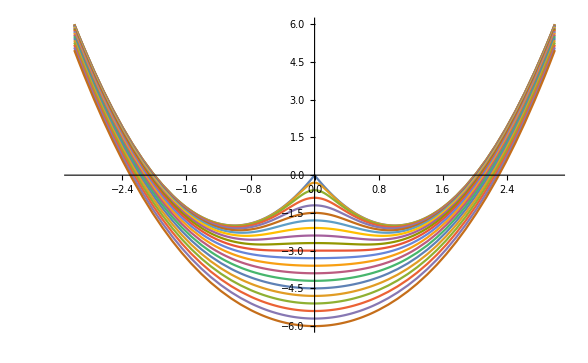

```mathematica
Plot[{{2 m^2+Eigenvalues[({{-4 m, 0., 0., 0.}, {0., 0, 0., 0.}, {0., 0., 0, 0.}, {0., 0., 0., 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.1, -0.1, -0.1}, {-0.1, 0, -0.1, -0.1}, {-0.1, -0.1, 0, -0.1}, {-0.1, -0.1, -0.1, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.2, -0.2, -0.2}, {-0.2, 0, -0.2, -0.2}, {-0.2, -0.2, 0, -0.2}, {-0.2, -0.2, -0.2, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.30000000000000004, -0.30000000000000004, -0.30000000000000004}, {-0.30000000000000004, 0, -0.30000000000000004, -0.30000000000000004}, {-0.30000000000000004, -0.30000000000000004, 0, -0.30000000000000004}, {-0.30000000000000004, -0.30000000000000004, -0.30000000000000004, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.4, -0.4, -0.4}, {-0.4, 0, -0.4, -0.4}, {-0.4, -0.4, 0, -0.4}, {-0.4, -0.4, -0.4, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.5, -0.5, -0.5}, {-0.5, 0, -0.5, -0.5}, {-0.5, -0.5, 0, -0.5}, {-0.5, -0.5, -0.5, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.6000000000000001, -0.6000000000000001, -0.6000000000000001}, {-0.6000000000000001, 0, -0.6000000000000001, -0.6000000000000001}, {-0.6000000000000001, -0.6000000000000001, 0, -0.6000000000000001}, {-0.6000000000000001, -0.6000000000000001, -0.6000000000000001, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.7000000000000001, -0.7000000000000001, -0.7000000000000001}, {-0.7000000000000001, 0, -0.7000000000000001, -0.7000000000000001}, {-0.7000000000000001, -0.7000000000000001, 0, -0.7000000000000001}, {-0.7000000000000001, -0.7000000000000001, -0.7000000000000001, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.8, -0.8, -0.8}, {-0.8, 0, -0.8, -0.8}, {-0.8, -0.8, 0, -0.8}, {-0.8, -0.8, -0.8, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -0.9, -0.9, -0.9}, {-0.9, 0, -0.9, -0.9}, {-0.9, -0.9, 0, -0.9}, {-0.9, -0.9, -0.9, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1., -1., -1.}, {-1., 0, -1., -1.}, {-1., -1., 0, -1.}, {-1., -1., -1., 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.1, -1.1, -1.1}, {-1.1, 0, -1.1, -1.1}, {-1.1, -1.1, 0, -1.1}, {-1.1, -1.1, -1.1, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.2000000000000002, -1.2000000000000002, -1.2000000000000002}, {-1.2000000000000002, 0, -1.2000000000000002, -1.2000000000000002}, {-1.2000000000000002, -1.2000000000000002, 0, -1.2000000000000002}, {-1.2000000000000002, -1.2000000000000002, -1.2000000000000002, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.3, -1.3, -1.3}, {-1.3, 0, -1.3, -1.3}, {-1.3, -1.3, 0, -1.3}, {-1.3, -1.3, -1.3, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.4000000000000001, -1.4000000000000001, -1.4000000000000001}, {-1.4000000000000001, 0, -1.4000000000000001, -1.4000000000000001}, {-1.4000000000000001, -1.4000000000000001, 0, -1.4000000000000001}, {-1.4000000000000001, -1.4000000000000001, -1.4000000000000001, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.5, -1.5, -1.5}, {-1.5, 0, -1.5, -1.5}, {-1.5, -1.5, 0, -1.5}, {-1.5, -1.5, -1.5, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.6, -1.6, -1.6}, {-1.6, 0, -1.6, -1.6}, {-1.6, -1.6, 0, -1.6}, {-1.6, -1.6, -1.6, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.7000000000000002, -1.7000000000000002, -1.7000000000000002}, {-1.7000000000000002, 0, -1.7000000000000002, -1.7000000000000002}, {-1.7000000000000002, -1.7000000000000002, 0, -1.7000000000000002}, {-1.7000000000000002, -1.7000000000000002, -1.7000000000000002, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.8, -1.8, -1.8}, {-1.8, 0, -1.8, -1.8}, {-1.8, -1.8, 0, -1.8}, {-1.8, -1.8, -1.8, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -1.9000000000000001, -1.9000000000000001, -1.9000000000000001}, {-1.9000000000000001, 0, -1.9000000000000001, -1.9000000000000001}, {-1.9000000000000001, -1.9000000000000001, 0, -1.9000000000000001}, {-1.9000000000000001, -1.9000000000000001, -1.9000000000000001, 4 m}}),1]},{2 m^2+Eigenvalues[({{-4 m, -2., -2., -2.}, {-2., 0, -2., -2.}, {-2., -2., 0, -2.}, {-2., -2., -2., 4 m}}),1]}},{m,-3,3}]
```

```mathematica
H4= -2m(KroneckerProduct[z,I2] + KroneckerProduct[I1,z,I1] + KroneckerProduct[I2,z]) -Δ(KroneckerProduct[x,I2]+ KroneckerProduct[I1,x,I1] + KroneckerProduct[I2,x] + τ KroneckerProduct[x,x,x])//MatrixForm
```

(-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ
-Δ | -2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0
-Δ | 0 | -2 m | -Δ | 0 | -Δ τ | -Δ | 0
0 | -Δ | -Δ | 2 m | -Δ τ | 0 | 0 | -Δ
-Δ | 0 | 0 | -Δ τ | -2 m | -Δ | -Δ | 0
0 | -Δ | -Δ τ | 0 | -Δ | 2 m | 0 | -Δ
0 | -Δ τ | -Δ | 0 | -Δ | 0 | 2 m | -Δ
-Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 6 m)

```mathematica
Ham = H4/.{τ-> 1}
```

(-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ
-Δ | -2 m | 0 | -Δ | 0 | -Δ | -Δ | 0
-Δ | 0 | -2 m | -Δ | 0 | -Δ | -Δ | 0
0 | -Δ | -Δ | 2 m | -Δ | 0 | 0 | -Δ
-Δ | 0 | 0 | -Δ | -2 m | -Δ | -Δ | 0
0 | -Δ | -Δ | 0 | -Δ | 2 m | 0 | -Δ
0 | -Δ | -Δ | 0 | -Δ | 0 | 2 m | -Δ
-Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 6 m)

```mathematica
δ =Range[0,2,.5];
```

```mathematica
Table[{Eigenvalues[Ham,1]/.{Δ->d2}}+3 m^2,{d2,δ}]
```

{{3 m^2+Eigenvalues[(-6 m | 0. | 0. | 0 | 0. | 0 | 0 | 0.
0. | -2 m | 0 | 0. | 0 | 0. | 0. | 0
0. | 0 | -2 m | 0. | 0 | 0. | 0. | 0
0 | 0. | 0. | 2 m | 0. | 0 | 0 | 0.
0. | 0 | 0 | 0. | -2 m | 0. | 0. | 0
0 | 0. | 0. | 0 | 0. | 2 m | 0 | 0.
0 | 0. | 0. | 0 | 0. | 0 | 2 m | 0.
0. | 0 | 0 | 0. | 0 | 0. | 0. | 6 m),1]},{3 m^2+Eigenvalues[(-6 m | -0.5 | -0.5 | 0 | -0.5 | 0 | 0 | -0.5
-0.5 | -2 m | 0 | -0.5 | 0 | -0.5 | -0.5 | 0
-0.5 | 0 | -2 m | -0.5 | 0 | -0.5 | -0.5 | 0
0 | -0.5 | -0.5 | 2 m | -0.5 | 0 | 0 | -0.5
-0.5 | 0 | 0 | -0.5 | -2 m | -0.5 | -0.5 | 0
0 | -0.5 | -0.5 | 0 | -0.5 | 2 m | 0 | -0.5
0 | -0.5 | -0.5 | 0 | -0.5 | 0 | 2 m | -0.5
-0.5 | 0 | 0 | -0.5 | 0 | -0.5 | -0.5 | 6 m),1]},{3 m^2+Eigenvalues[(-6 m | -1. | -1. | 0 | -1. | 0 | 0 | -1.
-1. | -2 m | 0 | -1. | 0 | -1. | -1. | 0
-1. | 0 | -2 m | -1. | 0 | -1. | -1. | 0
0 | -1. | -1. | 2 m | -1. | 0 | 0 | -1.
-1. | 0 | 0 | -1. | -2 m | -1. | -1. | 0
0 | -1. | -1. | 0 | -1. | 2 m | 0 | -1.
0 | -1. | -1. | 0 | -1. | 0 | 2 m | -1.
-1. | 0 | 0 | -1. | 0 | -1. | -1. | 6 m),1]},{3 m^2+Eigenvalues[(-6 m | -1.5 | -1.5 | 0 | -1.5 | 0 | 0 | -1.5
-1.5 | -2 m | 0 | -1.5 | 0 | -1.5 | -1.5 | 0
-1.5 | 0 | -2 m | -1.5 | 0 | -1.5 | -1.5 | 0
0 | -1.5 | -1.5 | 2 m | -1.5 | 0 | 0 | -1.5
-1.5 | 0 | 0 | -1.5 | -2 m | -1.5 | -1.5 | 0
0 | -1.5 | -1.5 | 0 | -1.5 | 2 m | 0 | -1.5
0 | -1.5 | -1.5 | 0 | -1.5 | 0 | 2 m | -1.5
-1.5 | 0 | 0 | -1.5 | 0 | -1.5 | -1.5 | 6 m),1]},{3 m^2+Eigenvalues[(-6 m | -2. | -2. | 0 | -2. | 0 | 0 | -2.
-2. | -2 m | 0 | -2. | 0 | -2. | -2. | 0
-2. | 0 | -2 m | -2. | 0 | -2. | -2. | 0
0 | -2. | -2. | 2 m | -2. | 0 | 0 | -2.
-2. | 0 | 0 | -2. | -2 m | -2. | -2. | 0
0 | -2. | -2. | 0 | -2. | 2 m | 0 | -2.
0 | -2. | -2. | 0 | -2. | 0 | 2 m | -2.
-2. | 0 | 0 | -2. | 0 | -2. | -2. | 6 m),1]}}

{0.173921+0. ⅈ,0.245634+0. ⅈ,0.326067+0. ⅈ}

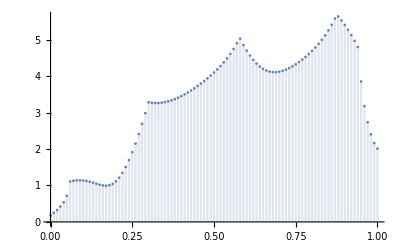

```mathematica
ClearAll[mat,minev]
SeedRandom[2]
rm=RandomInteger[10,{40,40,3}];

mat[t_]:=N[rm.{1,t,t^2}];
minev[t_?NumericQ]:=First@Eigenvalues[mat[t],-1];

Take[Table[minev[t],{t,0,1,.01}],3]

(*{-0.864071-1.30548 I,-0.861327-1.21718 I,-0.859129-1.12321 I}*)

DiscretePlot[Abs@minev[t],{t,0,1,.01}]
```

```mathematica
ClearAll[ev,minev]
```

```mathematica
ev[m_] := N[({{-6 m, 0, 0, 0, 0, 0, 0, 0}, {0, -2 m, 0, 0, 0, 0, 0, 0}, {0, 0, -2 m, 0, 0, 0, 0, 0}, {0, 0, 0, 2 m, 0, 0, 0, 0}, {0, 0, 0, 0, -2 m, 0, 0, 0}, {0, 0, 0, 0, 0, 2 m, 0, 0}, {0, 0, 0, 0, 0, 0, 2 m, 0}, {0, 0, 0, 0, 0, 0, 0, 6 m}})];
```

```mathematica
minev[m_?NumericQ]:=First@Eigenvalues[ev[m],-1];
```

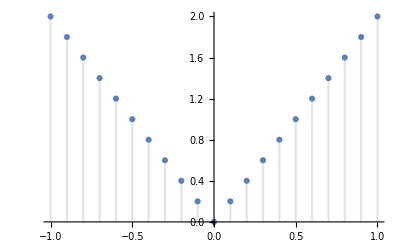

```mathematica
DiscretePlot[Abs@minev[m],{m,-1,1,0.1}]
```

```mathematica
H=Ham/.{Δ->0}
```

(-6 m | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 m | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 m | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 m | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 m | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 m | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 m | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 m)

```mathematica
ev[m_] := N[H];
```

```mathematica
minev[m_?NumericQ]:=First@Eigenvalues[ev[m],-1];
```

```mathematica
Take[Table[minev[m],{m,0,1,.1}],3]
```

{(0. | -0.5 | -0.5 | 0. | -0.5 | 0. | 0. | -0.5
-0.5 | 0. | 0. | -0.5 | 0. | -0.5 | -0.5 | 0.
-0.5 | 0. | 0. | -0.5 | 0. | -0.5 | -0.5 | 0.
0. | -0.5 | -0.5 | 0. | -0.5 | 0. | 0. | -0.5
-0.5 | 0. | 0. | -0.5 | 0. | -0.5 | -0.5 | 0.
0. | -0.5 | -0.5 | 0. | -0.5 | 0. | 0. | -0.5
0. | -0.5 | -0.5 | 0. | -0.5 | 0. | 0. | -0.5
-0.5 | 0. | 0. | -0.5 | 0. | -0.5 | -0.5 | 0.),(-0.6 | -0.5 | -0.5 | 0. | -0.5 | 0. | 0. | -0.5
-0.5 | -0.2 | 0. | -0.5 | 0. | -0.5 | -0.5 | 0.
-0.5 | 0. | -0.2 | -0.5 | 0. | -0.5 | -0.5 | 0.
0. | -0.5 | -0.5 | 0.2 | -0.5 | 0. | 0. | -0.5
-0.5 | 0. | 0. | -0.5 | -0.2 | -0.5 | -0.5 | 0.
0. | -0.5 | -0.5 | 0. | -0.5 | 0.2 | 0. | -0.5
0. | -0.5 | -0.5 | 0. | -0.5 | 0. | 0.2 | -0.5
-0.5 | 0. | 0. | -0.5 | 0. | -0.5 | -0.5 | 0.6),(-1.2 | -0.5 | -0.5 | 0. | -0.5 | 0. | 0. | -0.5
-0.5 | -0.4 | 0. | -0.5 | 0. | -0.5 | -0.5 | 0.
-0.5 | 0. | -0.4 | -0.5 | 0. | -0.5 | -0.5 | 0.
0. | -0.5 | -0.5 | 0.4 | -0.5 | 0. | 0. | -0.5
-0.5 | 0. | 0. | -0.5 | -0.4 | -0.5 | -0.5 | 0.
0. | -0.5 | -0.5 | 0. | -0.5 | 0.4 | 0. | -0.5
0. | -0.5 | -0.5 | 0. | -0.5 | 0. | 0.4 | -0.5
-0.5 | 0. | 0. | -0.5 | 0. | -0.5 | -0.5 | 1.2)}

```mathematica
DiscretePlot[Abs@minev[m],{m,0,1,0.1}]
```

-Graphics-